Graviational Field:

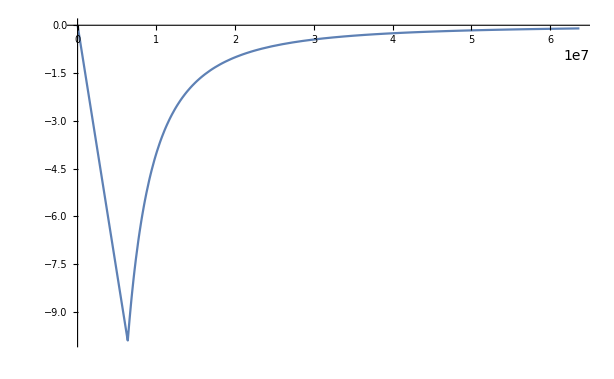

Graviational Potential:

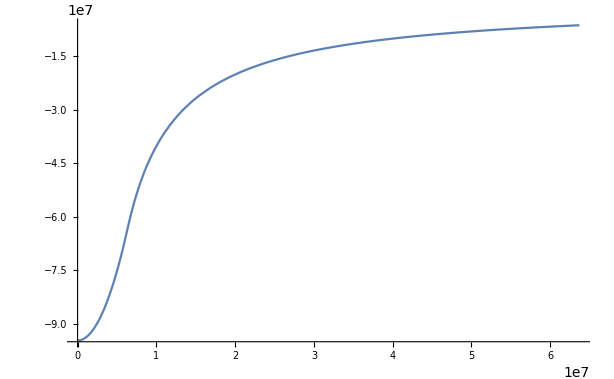

```mathematica
G=6.7*10^(-11);
M=6*10^24;
R=6371000;
"Graviational Field:"
Plot[If[x<R,-G M x/R^3,-G M/x^2],{x,0,10R},PlotRange->Full]
"Graviational Potential:"
Plot[If[x<R,G M(x^2-3R^2)/(2R^3),-G M/x],{x,0,10R},PlotRange->Full]
```